```mathematica
(* Cálculo de modos normales *)
l = 20;
g = 9.8;
m1 = 10;
m2 = 5;
tmat=0.5(l^2){{(m1+m2) ,m2 },{m2 ,m2 }};
vmat=0.5{{(m1+m2) g l,0},{0,m2 g l}};
m1 =tmat-(ω)vmat;
Solve[Det[m1]==0,ω]
N[Eigenvectors[{tmat-0.86255047104158*vmat}]]
```

{{ω→0.86255},{ω→3.21908}}

{{-0.866025,-0.5},{0.5,-0.866025}}

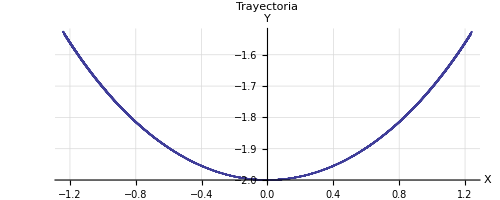

```mathematica
(* Gráfica de trayectoria con modo normal *)
tMax = 100;
With[{m1=10.0,
m2=5,
l=20.0,
g=9.81},sol = NDSolve[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == 0.5, θ2[0] ==0.8660254037844387, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->100]];
ParametricPlot[Evaluate[{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.sol],{t,0,tMax},AxesLabel->{Style["X", 15], Style["Y", 15]},PlotLabel->Style["Trayectoria", 15], GridLines->Automatic]
```